## 3.029 Data-Viz Hour 02/10/2022

Nature Scientific Data paper

https://www.nature.com/articles/s41597-020-0491-x

## Ionic Transport

Descriptors

```mathematica
descriptorsXLS=Import["/home/george/Downloads/Descriptors.xlsx"];
```

```mathematica
Dimensions[descriptorsXLS]
```

{4}

This means there are 4 sheets in the excel spreadsheet

```mathematica
Dimensions/@descriptorsXLS
```

{{1921,15},{2842,15},{1126,15},{1746,15}}

This means each sheet has 15 columns, but different number of rows

```mathematica
descriptorsXLS[[3,;;10]]//TableForm
```

Filename | Symmetry_space_group_name_H-M | R_T | R_Ta | R_Tb | R_Tc | IND | TCD | Acc_a | Acc_b | Acc_c | Recovery rate | Ionic_radii | Symmetry_Int_Tables_number | Minimal_mobile-framework_distance
icsd_000284.cif | C m c 21 | 0.738198 | 0.738198 | 0.604496 | 0.738198 | 3. | [] | True | True | True | 1. | {'O1': 1.24, 'O2': 1.21, 'V1': 0.67, 'Mg1': 0.8} | 36. | [(5, (1.9472206634773876, 0.7372206634773877))]
icsd_000394.cif | P 42/m n m | 0.587592 | 0.513876 | 0.513876 | 0.587592 | 1. | [1, 1] | False | False | True | 1. | {'F1': 1.16, 'Mg1': 0.86} | 136. | [(6, (1.979800570786313, 0.8198005707863132))]
icsd_000494.cif | P n m a | 0.577562 | 0.497091 | 0.577562 | 0.52201 | 1. | [1, 1] | False | True | False | 1. | {'O1': 1.22, 'O2': 1.22, 'Se1': 0.64, 'Mg1': 0.86} | 62. | [(6, (2.095432036182976, 0.8754320361829759))]
icsd_000625.cif | P 43 3 2 | 0.554848 | 0.554848 | 0.554848 | 0.554848 | 3. | [3] | True | True | True | 1. | {'O1': 1.24, 'O2': 1.24, 'Cu1': 0.74, 'Mn1': 0.67, 'Mg1': 0.86} | 212. | [(6, (2.0810872297671708, 0.8410872297671708))]
icsd_001086.cif | F d -3 m S | 0.45472 | 0.45472 | 0.45472 | 0.45472 | 0. | [] | False | False | False | 1. | {'O1': 1.24, 'Ge1': 0.53, 'Mg1': 0.86} | 227. | [(6, (2.0690207315037483, 0.8290207315037483))]
icsd_001314.cif | P 1 21/c 1 | 0.798752 | 0.604756 | 0.798752 | 0.798752 | 3. | [2, 2] | True | True | True | 1. | {'O1': 1.21, 'O2': 1.21, 'O3': 1.21, 'O4': 1.21, 'O5': 1.21, 'O6': 1.22, 'O7': 1.21, 'Mo1': 0.55, 'Mo2': 0.55, 'Mg1': 0.86} | 14. | [(6, (2.0304246238583645, 0.8204246238583646))]
icsd_002142.cif | P -3 m 1 | 1.80116 | 1.80116 | 1.80116 | 1.73693 | 3. | [] | True | True | True | 1. | {'Sb1': 0.9, 'Mg1': 0.86, 'Mg2': 0.86} | 164. | [(6, (3.111156985474346, 2.211156985474346)), (7, (2.8191964295046503, 1.9191964295046504))]
icsd_002321.cif | P -1 | 0.741217 | 0.48119 | 0.694772 | 0.741217 | 2. | [2] | False | True | True | 1. | {'O1': 1.22, 'O2': 1.22, 'O3': 1.21, 'O4': 1.22, 'O5': 1.22, 'O6': 1.22, 'O7': 1.22, 'V1': 0.495, 'V2': 0.495, 'Mg1': 0.86, 'Mg2': 0.86} | 2. | [(6, (1.9918066302164317, 0.7818066302164317)), (6, (2.048810719753874, 0.8288107197538739))]
icsd_002340.cif | P 63 m c | 0.603074 | 0.597228 | 0.20575 | 0.603074 | 2. | [] | True | False | True | 1. | {'O1': 1.26, 'O2': 1.26, 'Mg1': 0.71, 'K1': 1.51, 'K2': 1.69} | 186. | [(4, (1.993937999999999, 0.7339379999999991))]

We’ll stick with sheet 3

which is Magnesium

Good so far, we need to know how each structure looks like

So we will open the other dataset with the cif files

Post-mortem Note: We should’ve spent some more time looking at these descriptors

```mathematica
descriptorsXLS[[1,1]]
```

{Filename,Symmetry_space_group_name_H-M,R_T,R_Ta,R_Tb,R_Tc,IND,TCD,Acc_a,Acc_b,Acc_c,Recovery rate,Ionic_radii,Symmetry_Int_Tables_number,Minimal_mobile-framework_distance}

This helpful diagram from the paper helps define some of the interstice iimensions

E.g., one descriptor of interest is  R_T : the radius of the ‘bottleneck’ sphere (red in schematic above)

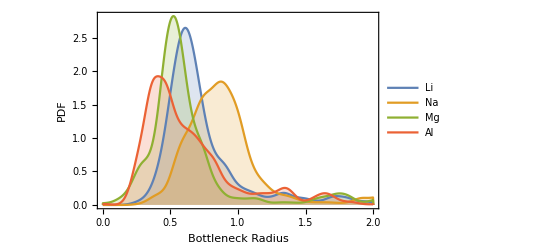

```mathematica
SmoothHistogram[AssociationThread[{"Li","Na","Mg","Al"},Select[#,NumberQ]&/@descriptorsXLS[[All,2;;,3]]],0.05,PlotRange->{{0,2},All},Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->18,Filling->Bottom,FrameLabel->{"Bottleneck Radius","PDF"}]
```

There’s also spacegroup information

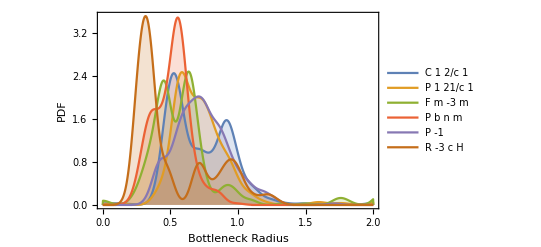

```mathematica
SmoothHistogram[Take[ReverseSortBy[KeySelect[GroupBy[Join@@descriptorsXLS[[All,2;;,{2,3}]],First][[All,All,2]],StringLength[#]>0&],Length],6],0.05,PlotRange->{{0,2},All},Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->18,Filling->Bottom,FrameLabel->{"Bottleneck Radius","PDF"}]
```

## Structure Files

Let’s have a look at how one of these VESTA files look like

```mathematica
exampleStructure=Import["/home/george/Downloads/Mg/icsd_002850.vesta","Data"]
```

{#VESTA_FORMAT_VERSION 3.3.0,,,CRYSTAL,,TITLE,./Li_Na_Mg_Al_cifs_order_revise_recover/Mg/icsd_002850,,GROUP,1 1 P 1,SYMOP, 0.000000  0.000000  0.000000  1  0  0   0  1  0   0  0  1   1, -1.0 -1.0 -1.0  0 0 0  0 0 0  0 0 0,TRANM 0,12610,SPLAN,  0   0   0   0,LBLAT,-1,LBLSP,-1,DLATM,-1,DLBND,-1,DLPLY,-1,PLN2D,0   0   0   0}
 |  |  |  |

By inspection, we’ve found that there’s relevant information about the cell type

Below the line “CELLP” (I’m assuming P here is for “primitive” cell)

```mathematica
Position[exampleStructure,"CELLP"]
```

{{29}}

These appear to be express in typical crystallographic specification

i.e. a,b,c, α, β, γ

```mathematica
{latticeParameters,latticeAnglesInDeg}=ToExpression[Partition[StringSplit[exampleStructure[[30]]," "],3]]
```

{{14.165,17.59,10.205},{90.,90.,90.}}

Note: we wrapped everything in “ToExpression” to convert strings into numbers

This is a utility function to convert from {a,b,c},{α,β,γ} to three 3D lattice vectors

```mathematica
latticeVectors[{a_,b_,c_},{α_,β_,γ_}]:=Simplify[{
{a,0,0},
{b Cos[γ], b Sin[γ],0},
{c Cos[β],c(Cos[α]-Cos[β]Cos[γ])/Sin[γ],√(c^2-(c Cos[β])^2-(c(Cos[α]-Cos[β]Cos[γ])/Sin[γ])^2)}
},{a,b,c}∈Reals]
```

Some examples:

Cubic

```mathematica
latticeVectors[{a,a,a},{π/2,π/2,π/2}]
```

{{a,0,0},{0,a,0},{0,0,Abs[a]}}

Hexagonal

```mathematica
latticeVectors[{a,a,c},{π/2,π/2,120°}]
```

{{a,0,0},{-a/2,(√3 a)/2,0},{0,0,Abs[c]}}

In our case

```mathematica
MatrixForm[
latticeVecs=Chop[latticeVectors[latticeParameters,latticeAnglesInDeg/180 π]]
]
```

(14.165 | 0 | 0
0 | 17.59 | 0
0 | 0 | 10.205)

Right about here we started running out of time

and frantically tried to get a visualization

i.e. the code below is rather messy, but given here “as-is” (with additional comments)

```mathematica
Position[exampleStructure,"SITET"]
```

{{9991}}

```mathematica
rows=Select[Take[exampleStructure[[33;;9989]],{1,-1,2}],Length[StringSplit[#]]>1&];
```

```mathematica
atLeastSevenHe=Select[StringSplit/@Select[rows,StringSplit[#][[2]]=="He"&],Length[#]>6&];
atLeastSevenNe=Select[StringSplit/@Select[rows,StringSplit[#][[2]]=="Ne"&],Length[#]>6&];
```

The lines above extract the lattice-coordinates “He” and “Ne” atoms

note they use He for interstices and Ne for bottlenecks

To convert from lattice-coordinates to Cartesian-coordinates, we take the dot product with our lattice vectors

```mathematica
heAtoms=ToExpression[atLeastSevenHe[[All,5;;7]]].latticeVecs;
neAtoms=ToExpression[atLeastSevenNe[[All,5;;7]]].latticeVecs;
```

```mathematica
Graphics3D[{Red,Point[heAtoms],Blue,Point[neAtoms]}]//Rasterize
```

-Graphics-

And then we said we’d try and visualize these “voids” slightly better using ‘point clouds’

```mathematica
Clear[pointCage]
pointCage[center_,radius_:0.25,n_:50]:=TranslationTransform[center]@*ScalingTransform[{1,1,1}radius]@SpherePoints[n]
```

```mathematica
Graphics3D[Point[pointCage[{0,0,0},1,500]]]
```

-Graphics3D-

```mathematica
Graphics3D[{Red,PointSize[Tiny],Point@*pointCage/@heAtoms,Blue,Point@*pointCage/@neAtoms}]//Rasterize
```

-Graphics-

Post-mortem Note: For what it’s worth, here’s how a more complete VESTA file parser might look like

```mathematica
Clear[vestaRead]
```

```mathematica
vestaRead[icsdId_]:=Block[{
vestaData,cellPosition,latVecs,lengths,angles,structPosition,theriPosition,atomicData,atoms,directCoords,dups,ints,labelsAsc,bondsPosition,tetPosition,bondData,bonds,vectrPosition,radii
},
vestaData=Import[StringTemplate["/home/george/Downloads/Mg/icsd_`1`.vesta"][IntegerString[icsdId,10,6]],"Table"];
cellPosition=Position[vestaData,"CELLP"][[1,1]];
{lengths,angles}=Partition[vestaData[[cellPosition+1]],3];
latVecs=Chop[latticeVectors[lengths,angles π/180]];

structPosition=Position[vestaData,"STRUC"][[1,1]];
theriPosition=Position[vestaData,"THERI"][[1,1]];

atomicData=Take[vestaData,{structPosition+1,theriPosition-2,2}];
atoms=atomicData[[All,2]];

directCoords=Mod[atomicData[[All,5;;7]],1];
dups=DeleteDuplicates[atoms];

ints=atoms/.Thread[dups->Range[Length[dups]]];
labelsAsc=AssociationThread[atomicData[[All,3]]->Range[Length[atoms]]];

bondsPosition=Position[vestaData,"SBOND"][[1,1]];
tetPosition=Position[vestaData,"SITET"][[1,1]];

bondData=Take[vestaData,{bondsPosition+1,tetPosition-2}];
bonds=bondData[[All,{2,3}]];
bonds=Lookup[labelsAsc,#]&/@bonds;

vectrPosition=Position[vestaData,"VECTR"][[1,1]];
radii=vestaData[[tetPosition+1;;vectrPosition-2,3]];

{latVecs,directCoords,dups,ints,bonds,radii}
]
```

This returns the following:

lattice-vectors (3X3 matrix)

direct-coordinates (Nx3 array)

void type (note they use He for interstices and Ne for bottlenecks)

identification of each void according to type (N integers)

channel segments represented as bonds b/w two void sites (Mx2 array)

void space radii (N reals)

```mathematica
Graphics3D[{If[#3==1,{Blue,Sphere[#1,#2/2]},{RGBColor[0,0.33,0],Sphere[#1,#2/2]}]&@@@(Transpose[{#2.#1,#6,#4}]&@@vestaRead[2850])},ImageSize->350]//Rasterize
```

-Graphics-